```mathematica
(* Global Representation Space (GRS) ; 
   θY A p Subscript[y, 0] d Lcur ;       
   1  2 3 4  5  6  ; *)
```

```mathematica
Clear[Bo,θY];
zero[p_?NumberQ,y0_?NumberQ,dsup_?NumberQ,Lcur_?NumberQ]:=Block[
{sol,s,y,a,x,θ},
sol=NDSolve[
{(*equation d'energie *)
-θ'[s]==p-y[s]*Bo,
a'[s]==2*y[s]*Cos[θ[s]],
y'[s]==Sin[θ[s]],
x'[s]==Cos[θ[s]],

(*Conditions au s = 0*)
a[0]==0,
x[0]== 0,
θ[0]== 0,
y[0]==y0},

{y[s],a[s],θ[s],x[s]},{s,0,Lcur}
];

(*conditions de bords*)
{y[s],a[s]-A,θ[s]+θY,x[s] - dsup}/.sol[[1]]/.s->Lcur
]
```

```mathematica
θY=Pi;
Bo=1.1;
Rc=1.0;
A=Pi * Rc^2;
grsdepart={0.1,A,2.083704188430398,1.499047813912092,0.7598910513142646,2.583053913047227};
listeGRS={grsdepart}; 
dernierpointtrouve=listeGRS[[-1]];
papprox=dernierpointtrouve[[3]];
y0approx=dernierpointtrouve[[4]];
dapprox=dernierpointtrouve[[5]];
Lapprox = dernierpointtrouve[[6]];
```

```mathematica
fr=FindRoot[zero[p,y0,dsup,Lcur],{p,papprox},{y0,y0approx},{dsup,dapprox},{Lcur,Lapprox},
MaxIterations->100,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];
Print[{p,y0,dsup,Lcur}/.fr];
```

{2.17054,1.46604,0.796058,2.55668}

```mathematica
erreur=Total[Abs[zero[p/.fr,y0/.fr,dsup/.fr,Lcur/.fr]]]
```

1.30603×10^-13

Verifier le forme

```mathematica
Lplot=Lcur/.fr;
pplot=p/.fr;
y0plot=y0/.fr;
Print["Lplot:",Lplot,"/pplot:",pplot,"/y0plot:",y0plot]
```

Lplot:2.55668/pplot:2.17054/y0plot:1.46604

```mathematica
solforme=NDSolve[{p'[s]==0,-θ'[s]==p[s]-y[s]*Bo,y'[s]==Sin[θ[s]],x'[s]==Cos[θ[s]],a'[s]== 2*y[s]*Cos[θ[s]],
a[0]==0,
θ[0]== 0,

a[L]==A,
y[L]== 0,
θ[L]==-Pi}/.L->Lplot,{y,p,a,x,θ},s,
Method->{"Shooting", "StartingInitialConditions"->{a[0]==0,x[0]== 0,p[0]==pplot,y'[0] == 0,y[0] ==y0plot}}]
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

NDSolve::berr: The scaled boundary value residual error of 3.62407 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{y→InterpolatingFunction[…],p→InterpolatingFunction[…],a→InterpolatingFunction[…],x→InterpolatingFunction[…],θ→InterpolatingFunction[…]}}

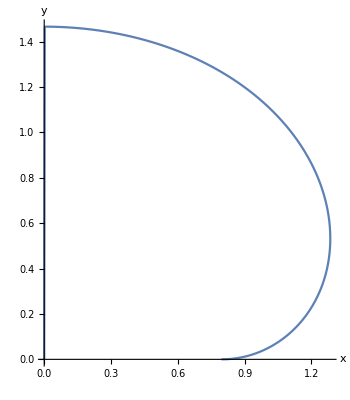

```mathematica
Listdata={{0,0}};
Do[
ss=Lplot*i/1000;
new={x[ss],y[ss]}/.solforme[[1]];
AppendTo[Listdata,new],
{i,1,1000,1}]
plotnumerique=ListLinePlot[Listdata,AxesLabel-> {Style["x",FontSize->22],Style["y",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->Automatic]
```